```mathematica
ContourPlot3D[50+((0.04*x*y*0.5)/(0.0745*6.4516))*((1+(3*(3.1415^0.5)/4)*0.5*0.05*(y/(0.6962*1))^0.5)^-1)-z,{x,-2,2},{y,-2,2},{z,-2,2},Contours->5,Mesh->None]
```

-Graphics3D-

```mathematica
ContourPlot[50+((0.04*x*y*0.5)/(0.0745*6.4516))*((1+(3*(3.1415^0.5)/4)*0.5*0.05*(y/(0.6962*1))^0.5)^-1)-z,{x,0,65000},{y,0,350},{z,0,1000},Contours->5,Mesh->None]
```

ContourPlot::nonopt: Options expected (instead of {z,0,1000}) beyond position 3 in ContourPlot[50+(0.04 x y 0.5)/((0.0745 6.4516) (1+(3 «2») 0.5 0.05 Times[«2»]^0.5))-z,{x,0,65000},{y,0,350},{z,0,1000},Contours→5,Mesh→None]. An option must be a rule or a list of rules.

ContourPlot[50+(0.04 x y 0.5)/((0.0745 6.4516) (1+1/4 (3 3.1415^0.5) 0.5 0.05 (y/(0.6962 1))^0.5))-z,{x,0,65000},{y,0,350},{z,0,1000},Contours→5,Mesh→None]

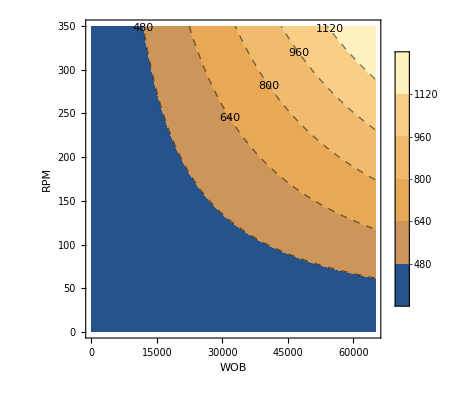

```mathematica
Amin1=ContourPlot[300+((0.04*x*0.1390069*y*0.007993487*0.5)/(0.0745*6.4516))*((1+(3*(3.1415^0.5)/4)*0.5*0.05*(y*0.007993487/(0.6962*1))^0.5)^-1),{x,0,65000},{y,0,350},Contours->5,PlotLegends->Automatic,ContourLabels->All,ContourStyle->Dashed,AxesLabel->{WOB,RPM}]
```

```mathematica
d1=50+((0.04*x*0.1390069*y*0.007993487*0.5)/(0.0745*6.4516))*((1+(3*(3.1415^0.5)/4)*0.5*0.05*(y*0.007993487/(0.6962*1))^0.5)^-1)
```

```mathematica
ListPointPlot3D[Table[s1,{x,0,65000,1000},{y,0,350,10}]]
```

-Graphics3D-

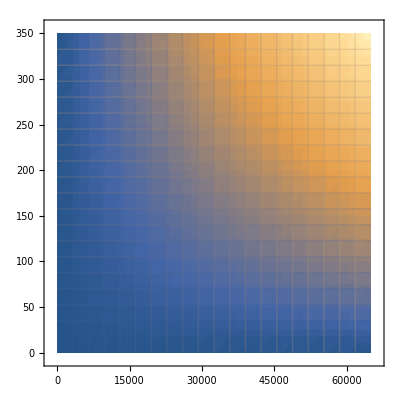

```mathematica
DensityPlot[50+((0.04*x*0.1390069*y*0.007993487*0.5)/(0.0745*6.4516))*((1+(3*(3.1415^0.5)/4)*0.5*0.05*(y*0.007993487/(0.6962*1))^0.5)^-1),{x,0,65000},{y,0,350},Mesh->19]
```

```mathematica
Plot3D[50+((0.04*x*0.1390069*y*0.007993487*0.5)/(0.0745*6.4516))*((1+(3*(3.1415^0.5)/4)*0.5*0.05*(y*0.007993487/(0.6962*1))^0.5)^-1),{x,0,65000},{y,0,350}]
```

-Graphics3D-

```mathematica
Plot3D[50+(0.04 x 0.1390069 y 0.007993487 0.5)/((0.0745 6.4516) (1+1/4 (3 3.1415^0.5) 0.5 0.05 ((y 0.007993487)/(0.6962 1))^0.5)),{x,0,65000},{y,0,350},PlotStyle->Directive[GrayLevel[0],Opacity[0.672]]]
```

-Graphics3D-

```mathematica
DensityPlot3D[50+((0.04*x*y*0.5)/(0.0745*6.4516))*((1+(3*(3.1415^0.5)/4)*0.5*0.05*(y/(0.6962*1))^0.5)^-1)-z,{x,0,65000},{y,0,350},{z,0,1000}]
```

-Graphics3D-

```mathematica
SliceContourPlot3D[50+((0.04*x*y*0.5)/(0.0745*6.4516))*((1+(3*(3.1415^0.5)/4)*0.5*0.05*(y/(0.6962*1))^0.5)^-1)-z,"CenterPlanes",{x,0,65000},{y,0,350},{z,0,1000}]
```

-Graphics3D-

```mathematica
ListPointPlot3D[Table[Sin[j^2+i],{i,0,3,0.1},{j,0,3,0.1}]]
```

-Graphics3D-

```mathematica
ListPointPlot3D[Table[Sin[j^2+i],{i,0,3,0.1},{j,0,3,0.1}]]
```

```mathematica
data=Table[10 i+j,{i,4},{j,3}]
```

{{11,12,13},{21,22,23},{31,32,33},{41,42,43}}

```mathematica
data
```

{{11,12,13},{21,22,23},{31,32,33},{41,42,43}}

```mathematica
data=Table[50+((0.04*x*y*0.5)/(0.0745*6.4516))*((1+(3*(3.1415^0.5)/4)*0.5*0.05*(y/(0.6962*1))^0.5)^-1)-z,"CenterPlanes",{x,0,65000},{y,0,350}]
```

Table::iterb: Iterator {CenterPlanes} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Table[50+(0.04 x y 0.5)/((0.0745 6.4516) (1+1/4 (3 3.1415^0.5) 0.5 0.05 (y/(0.6962 1))^0.5))-z,{CenterPlanes},{x,0,65000},{y,0,350}]

```mathematica
data=Table[50+((0.04*x*y*0.5)/(0.0745*6.4516))*((1+(3*(3.1415^0.5)/4)*0.5*0.05*(y/(0.6962*1))^0.5)^-1),"CenterPlanes",{x,0,65000},{y,0,350}]
```

Table::iterb: Iterator {CenterPlanes} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Table[50+(0.04 x y 0.5)/((0.0745 6.4516) (1+1/4 (3 3.1415^0.5) 0.5 0.05 (y/(0.6962 1))^0.5)),{CenterPlanes},{x,0,65000},{y,0,350}]

```mathematica
data=Table[50+((0.04*x*y*0.5)/(0.0745*6.4516))*((1+(3*(3.1415^0.5)/4)*0.5*0.05*(y/(0.6962*1))^0.5)^-1)-z,"CenterPlanes",{x,65000},{y,350}]
```

Table::iterb: Iterator {CenterPlanes} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Table[50+(0.04 x y 0.5)/((0.0745 6.4516) (1+1/4 (3 3.1415^0.5) 0.5 0.05 (y/(0.6962 1))^0.5))-z,{CenterPlanes},{x,65000},{y,350}]

```mathematica
data=Table[50+((0.04*x*y*0.5)/(0.0745*6.4516))*((1+(3*(3.1415^0.5)/4)*0.5*0.05*(y/(0.6962*1))^0.5)^-1),"CenterPlanes",{x,65000},{y,350}]
```

Table::iterb: Iterator {CenterPlanes} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Table[50+(0.04 x y 0.5)/((0.0745 6.4516) (1+1/4 (3 3.1415^0.5) 0.5 0.05 (y/(0.6962 1))^0.5)),{CenterPlanes},{x,65000},{y,350}]

```mathematica
data=Table[50+((0.04*x*y*0.5)/(0.0745*6.4516))*((1+(3*(3.1415^0.5)/4)*0.5*0.05*(y/(0.6962*1))^0.5)^-1),{x,65000},{y,350}]
```

$Aborted

```mathematica
data=Table[50+((0.04*x*y*0.5)/(0.0745*6.4516))*((1+(3*(3.1415^0.5)/4)*0.5*0.05*(y/(0.6962*1))^0.5)^-1),{x,65000,1000},{y,350,50}]
```

{}

```mathematica
data
```

{}

```mathematica
Information[data]
```

Global`data

data={}

```mathematica
ListPointPlot3D[Table[50+((0.04*x*0.1390069*y*0.007993487*0.5)/(0.0745*6.4516))*((1+(3*(3.1415^0.5)/4)*0.5*0.05*(y*0.007993487/(0.6962*1))^0.5)^-1),{x,0,65000,1000},{y,0,350,5}],ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
DiscretePlot3D[50+((0.04*x*0.1390069*y*0.007993487*0.5)/(0.0745*6.4516))*((1+(3*(3.1415^0.5)/4)*0.5*0.05*(y*0.007993487/(0.6962*1))^0.5)^-1),{x,0,65000,5000},{y,0,350,30},ExtentSize->Full,ColorFunction->"Rainbow",AxesLabel->{WOB,RPM,Tw}]
```

-Graphics3D-

```mathematica
DiscretePlot3D[50+(0.04 x 0.1390069 y 0.007993487 0.5)/((0.0745 6.4516) (1+1/4 (3 3.1415^0.5) 0.5 0.05 ((y 0.007993487)/(0.6962 1))^0.5)),{x,0,65000,5000},{y,0,350,30},PlotTheme->Automatic,ExtentSize->Full,ColorFunction->"Rainbow",AxesLabel->{WOB,RPM,Tw}]
```

-Graphics3D-

```mathematica
DiscretePlot3D[50+(0.04 x 0.1390069 y 0.007993487 0.5)/((0.0745 6.4516) (1+1/4 (3 3.1415^0.5) 0.5 0.05 ((y 0.007993487)/(0.6962 1))^0.5)),{x,0,65000,5000},{y,0,350,30},ExtentSize->Full,ExtentElementFunction->"Cube",PlotTheme->Automatic,ColorFunction->"Rainbow",AxesLabel->{WOB,RPM,Tw}]
```

-Graphics3D-

```mathematica
Show[%49,ImageSize->Medium]
```

-Graphics3D-

```mathematica
Show[%51,ImageSize->Full]
```

```mathematica
Show[%53,ImageSize->Large]
```

-Graphics3D-

```mathematica
Show[%54,ViewPoint->Above]
```

-Graphics3D-

```mathematica
Show[%62,ViewPoint->{1.3,-2.4,2.}]
```

-Graphics3D-

```mathematica
Show[%63,ViewPoint->Right]
```

-Graphics3D-

```mathematica
Show[%64,ViewPoint->Front]
```

-Graphics3D-

```mathematica
Show[%64,ViewPoint->Below]
```

-Graphics3D-

```mathematica
Show[%64,ViewPoint->Back]
```

-Graphics3D-

```mathematica
Show[%65,ViewPoint->{0,0,∞}]
```

-Graphics3D-

```mathematica
Show[%68,Boxed->False]
```

-Graphics3D-

```mathematica
Show[%69,ViewPoint->{0,0,∞}]
```

-Graphics3D-

```mathematica
Show[%70,ViewPoint->{0,0,∞}]
```

-Graphics3D-

```mathematica
f3=150+((0.04*x*0.1390069*y*0.007993487*0.5)/(0.0745*6.4516))*((1+(3*(3.1415^0.5)/4)*0.5*0.05*(y*0.007993487/(0.6962*1))^0.5)^-1)
```

150+(0.0000462359 x y)/(1+0.00356099 y^0.5)

```mathematica
DiscretePlot3D[f3,{x,0,65000,5000},{y,0,350,30},ExtentSize->Full,PlotStyle->EdgeForm[],AxesLabel->{WOB,RPM,Tw}]
```

-Graphics3D-

```mathematica
DiscretePlot3D[f3,{x,0,65000,5000},{y,0,350,30},ExtentElementFunction->Automatic,ExtentSize->Full,PlotStyle->EdgeForm[],ColorFunction->Function[{x,y,z},Hue[z]],AxesLabel->{WOB,RPM,Tw}]
```

-Graphics3D-

```mathematica
Rasterize[%18,"Image"]
```

```mathematica
Rasterize[%18,"Image"]
```

```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
DensityPlot3D[50+((0.04*x*0.1390069*y*0.007993487*0.5)/(0.0745*6.4516))*((1+(3*(3.1415^0.5)/4)*0.5*0.05*(y*0.007993487/(0.6962*1))^0.5)^-1),{x,0,65000},{y,0,350},{z,0,1000}]
```

-Graphics3D-

```mathematica
f=50+((0.04*x*0.1390069*y*0.007993487*0.5)/(0.0745*6.4516))*((1+(3*(3.1415^0.5)/4)*0.5*0.05*(y*0.007993487/(0.6962*1))^0.5)^-1)
DensityPlot3D[f,{x,0,65000},{y,0,350},{z,0,1000},ColorFunction->"SunsetColors",PlotLegends->Automatic,OpacityFunction->None]
```

50+(0.0000462359 x y)/(1+0.00356099 y^0.5)

-Graphics3D-

```mathematica
a=50+(0.00004623585796147337 x y)/(1+0.0035609914515185035 y^0.5);
a
```

50+(0.0000462359 x y)/(1+0.00356099 y^0.5)

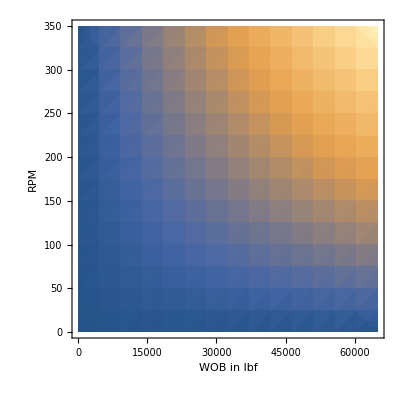

```mathematica
CDen1=DensityPlot[50+(0.00004623585796147337 x y)/(1+0.0035609914515185035 y^0.5),{x,0,65000},{y,0,350},FrameLabel->{"WOB in lbf","RPM"}]
```

```mathematica
s1=50+((0.04*x*0.1390069*y*0.007993487*0.5)/(0.0745*6.4516))*((1+(3*(3.1415^0.5)/4)*0.5*0.05*(y*0.007993487/(0.6962*1))^0.5)^-1)
```

50+(0.0000462359 x y)/(1+0.00356099 y^0.5)

```mathematica
ListPointPlot3D[{Table[s1,{x,0,65000,2000},{y,0,350,10}],Table[s2,{x,0,65000,2000},{y,0,350,10}]}]
```

-Graphics3D-

```mathematica
Plot3D[{50+((0.04*x*0.1390069*y*0.007993487*0.5)/(0.0745*6.4516))*((1+(3*(3.1415^0.5)/4)*0.5*0.05*(y*0.007993487/(0.6962*1))^0.5)^-1),50+((0.04*x*0.1390069*y*0.007993487*0.5)/(0.0745*6.4516))*((1+(3*(3.1415^0.5)/4)*0.5*0.05*(y*0.007993487/(0.6962*1))^0.5)^-1)},
{x,0,65000},{y,0,350}]
```

-Graphics3D-

General::stop: Further output of Plot3D::pllim will be suppressed during this calculation.

```mathematica
s1=50+((0.04*x*0.1390069*y*0.007993487*0.5)/(0.0745*6.4516))*((1+(3*(3.1415^0.5)/4)*0.5*0.05*(y*0.007993487/(0.6962*1))^0.5)^-1)
```

50+(0.0000462359 x y)/(1+0.00356099 y^0.5)

```mathematica
s2=50+((0.04*(65000-x)*0.1390069*(350-y)*0.007993487*0.5)/(0.0745*6.4516))*((1+(3*(3.1415^0.5)/4)*0.5*0.05*((350-y)*0.007993487/(0.6962*1))^0.5)^-1)
```

50+(0.0000462359 (65000-x) (350-y))/(1+0.00356099 (350-y)^0.5)

```mathematica
s3=50+((0.04*(x)*0.1390069*(350-y)*0.007993487*0.5)/(0.0745*6.4516))*((1+(3*(3.1415^0.5)/4)*0.5*0.05*((350-y)*0.007993487/(0.6962*1))^0.5)^-1)
```

50+(0.0000462359 x (350-y))/(1+0.00356099 (350-y)^0.5)

```mathematica
ContourPlot[{s1==650,s1==750,s1==950,s2==800,s2==500,s3==800}
,{x,0,65000},{y,0,350},FrameLabel->{"WOB in lbf","RPM"}]
```

-Graphics-

```mathematica
C1=ContourPlot[{s1==380},{x,0,65000},{y,0,350},FrameLabel->{"WOB in lbf","RPM"},ContourLabels->True];
C2=ContourPlot[{s1==550},{x,0,65000},{y,0,350},FrameLabel->{"WOB in lbf","RPM"},ContourLabels->True];
C3=ContourPlot[{s2==650},{x,0,65000},{y,0,350},FrameLabel->{"WOB in lbf","RPM"},ContourLabels->True,ContourStyle->Black];
C4=ContourPlot[{s3==650},{x,0,65000},{y,0,350},FrameLabel->{"WOB in lbf","RPM"},ContourLabels->True,ContourStyle->Black];


CDen1=DensityPlot[180+(0.00004623585796147337 x y)/(1+0.0035609914515185035 y^0.5),{x,0,65000},{y,0,350},FrameLabel->{"WOB in lbf","RPM"},
Mesh->All,AspectRatio->0.78,ColorFunction->"SunsetColors",PlotLegends->BarLegend[Automatic,
LegendMarkerSize->180,LegendFunction->"Frame",LegendMargins->5,
LegendLabel->"Tw in C"],PlotLegends->Automatic];
Amin1=ContourPlot[300+((0.04*x*0.1390069*y*0.007993487*0.5)/(0.0745*6.4516))*((1+(3*(3.1415^0.5)/4)*0.5*0.05*(y*0.007993487/(0.6962*1))^0.5)^-1),{x,0,65000},{y,0,350},Contours->10,PlotLegends->Automatic,ContourLabels->All,ContourStyle->Dashed,FrameLabel->{"WOB in lbf","RPM"},ColorFunction->"SunsetColors",PlotLabel->"The Cutter Wear Flat Area Temperature vs WOB and RPM",AspectRatio->1/1.5];
s11=Graphics[{Text[Bit Jumping,{55000,50}],Text[Stick-Slip,{10000,50}]}];
Show[CDen1,C3,C4,s11];
Show[Amin1,C3,C4,s11]
```